P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,p_]:=((l1+l2+c-1)!)/(2^(l1+l2)(c-1)!l1!l2!)*p^(l1+l2)(1-p)^c
```

P(l1=L1,l2<L2)    P(l1<L1, l2=L2)

```mathematica
PLl2[L1_,l2_,c_,p_]:=1-Sum[P1[l1,l2,c,p],{l1,0,L1-1}]
PLl1[l1_,L2_,c_,p_]:=1-Sum[P1[l1,l2,c,p],{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P2[L1_,L2_,c_,p_]:=1-Sum[Sum[P1[l1,l2,c,p],{l1,0,L1-1}],{l2,0,L2}]-P1[L1,L2-1,c,p]
```

Note that also L2 Cannot be less than 1.

```mathematica
En[L1_,L2_,c_,p_]:=-(Sum[Sum[P1[l1,l2,c,p]*Log[P1[l1,l2,c,p]],{l1,0,L1-1}],{l2,0,L2}]+P1[L1,L2-1,c,p]*Log[P1[L1,L2-1,c,p]]+P2[L1,L2,c,p]*Log[P2[L1,L2,c,p]])
```

For comparison P(l<L, c=1)

```mathematica
P11[l_,p_]:=(1-p)* p^l
```

P(l=L,c=1)

```mathematica
P21[L_,p_]:=p^L
```

Entropy c=1

```mathematica
EN[L_,p_]:=-(Sum[P11[l,p]*Log[P11[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

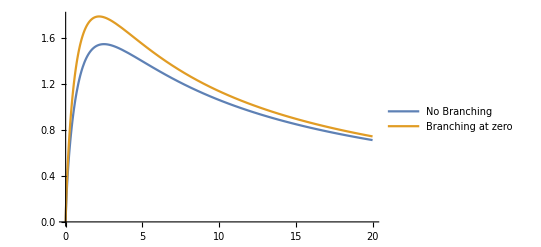

```mathematica
Plot[{EN[4,h[τ]],En[4,1,1,h[τ]]},{τ,0,20},PlotLegends->{"No Branching","Branching at zero"}]
```

Two Compartments

P(l<L,c=2)

```mathematica
P12[l_,p_]:=(1-p)^2*(1+l) p^l
```

P(l=L,c=2)

```mathematica
P22[L_,p_]:=1-(1-p)^2*(-(L p^L)/(1-p)+(1-p^L)/(1-p)+(p (1-p^L))/(1-p)^2)
```

Entropy c=2

```mathematica
EN2[L_,p_]:=-(Sum[P12[l,p]*Log[P12[l,p]],{l,0,L-1}]+P22[L,p]*Log[P22[L,p]])
```

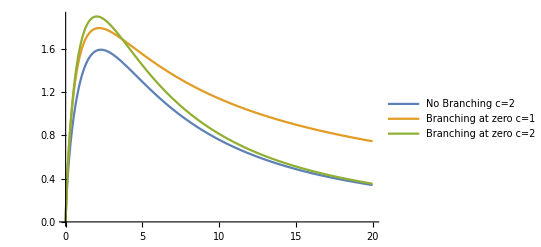

```mathematica
Plot[{EN2[4,h[τ/2]],En[4,1,1,h[τ]],En[4,1,2,h[τ/2]]},{τ,0,20},PlotLegends->{"No Branching c=2","Branching at zero c=1","Branching at zero c=2"}]
```

Entropy slightly INCREASES with more Compartments, but yield of terminal structure is higher with more compartments??!?!

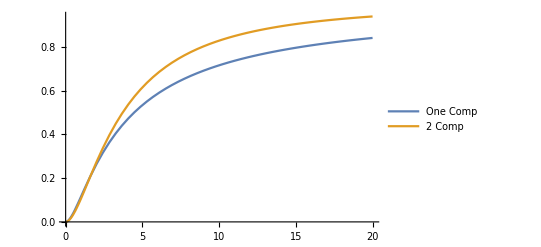

```mathematica
Plot[{P2[4,1,1,h[τ]],P2[4,1,2,h[τ/2]]},{τ,0,20},PlotLegends->{"One Comp","2 Comp"}]
```

2 Length fours, not much more

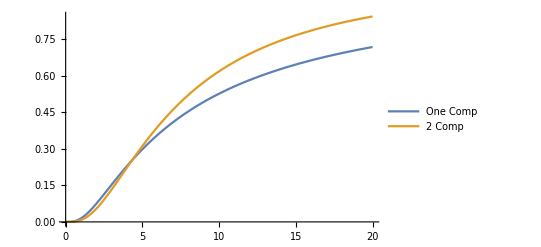

```mathematica
Plot[{P2[4,4,1,h[τ]],P2[4,4,2,h[τ/2]]},{τ,0,20},PlotLegends->{"One Comp","2 Comp"}]
```

checking the yields for different species

```mathematica
L1=4;
L2=1;
c=1;
T1=Evaluate@Table[P1[l1,l2,c,p], {l1,0,L1-1},{l2,0,L2-1}];
T2=Evaluate@Table[
```

{2^-l2 (1-p) p^l2,(2^(-1-l2) (1-p) p^(1+l2) (1+l2)!)/(l2!),(2^(-3-l2) (1-p) p^(2+l2) (2+l2)!)/(l2!),(2^(-4-l2) (1-p) p^(3+l2) (3+l2)!)/(3 l2!),(2^(-7-l2) (1-p) p^(4+l2) (4+l2)!)/(3 l2!)}